# Plot

## Setup

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
rootdir = Directory[];

imgsize = Large;

nstep=20;
n = (nstep+1)^2;

data = Import["./export/lambda-omega-k1-k2_2D.dat"];

{Nr, Nc} = Dimensions[data]
```

{1323,9}

```mathematica
showdata=Prepend[data, { "k_1", "k_2","λ", "ω_1/ω_ref", "ω_2/ω_ref", "ω_3/ω_ref", "ω_4/ω_ref", "ω_5/ω_ref", "ω_6/ω_ref"} ]//TableForm;
```

## Plot dispersion surfaces depending on λ

```mathematica
Clear[l];
plot1[λ_]:=Module[{},
If[λ==10,l=1, If[λ==20, l=2, l=3]];
Show[
ListPlot3D[
Table[
Transpose[{data[[i, 2]], data[[i, 3]], data[[i, j]]}],
{j, 4, Nc},{i, (l-1)*n+1, l*n}
],
 AxesLabel->{"k_1 [m^-1]", "k_2 [m^-1]","ω/ω_ref [-]" }, Mesh->Automatic, ImageSize->imgsize,  ImageSize->imgsize, PlotLabel->Text[Style[HoldForm["λ" = λ], FontSize->18]],
BoxRatios->{1, 1, 2}, PlotStyle->Automatic,
PlotRange->{Automatic,Automatic, {0,4.5}},
Ticks->{Table[k,{k,0,Pi,Pi/4}],Table[k,{k,0,Pi,Pi/4}],Automatic},
PlotTheme->"Scientific"
]
(*,ParametricPlot3D[{x,y,1}, {x, 0, Pi}, {y, 0, Pi}, 
PlotStyle->{Gray, Opacity[.5]},
Mesh->None]*)
]
]
(*GraphicsRow[{plot1[10], plot1[20], plot1[50]}, Spacings->10, ImageSize->1200, ImagePadding->0]*)
plot1[20]
```

-Graphics3D-

## Plot single dispersion surface

```mathematica
l=2;
Grid[{{
Table[
ListPlot3D[
Table[
Transpose[{data[[i, 2]], data[[i, 3]], data[[i, j]]}],
{i, (l-1)*n+1, l*n}
],
 AxesLabel->{"k_1 [m^-1]", "k_2 [m^-1]","ω/ω_ref [-]" }, Mesh->Automatic, ImageSize->350, PlotLabel->Text[Style["Dispersion surface " <>ToString[j-3], FontSize->18]],
ColorFunction->"Rainbow", PlotLegends->Automatic
,BoxRatios->{1, 1, 2}, 
PlotStyle->Automatic, 
InterpolationOrder->4,
PlotRange->{{0,Pi}, {0,Pi}, {0,4}},
Ticks->{Table[k, {k,0,Pi, Pi/4}], Table[k, {k,0,Pi, Pi/4}], Automatic},
PlotTheme->"Scientific"
],
{j,4,Nc}]
}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Differences tabs

## Import

```mathematica
disp = SetPrecision[Import["./export/displacement_comparison.dat"],20]
```

{{0,1.4100000000017220706×10^-6,1.4099172708589951816×10^-6,6.6427926825847073548×10^-7,1.0028020476826872411×10^-7,1.4067931653990983195×10^-6,1.4088126883611134754×10^-6},{1.,1.4100000000008316273×10^-6,1.4099876467158740501×10^-6,6.6396087499679701966×10^-7,6.4824279091197972372×10^-7,1.4096193928226308383×10^-6,1.4096315954939080541×10^-6},{2.,1.4099998270123264015×10^-6,1.4100000022815870576×10^-6,6.6328586510546739521×10^-7,6.6385741043981401451×10^-7,1.4099983350048687934×10^-6,1.4099497755791766451×10^-6}}

```mathematica
omega = SetPrecision[Import["./export/omega_comparison.dat"],20]
```

{{0,0.48008454294971353304,1.2148236450626297422,2.0740726743617883265,2.0741222686402691622,3.1907050215225725154,3.2669218950066998275},{1.,0.48000292845674508158,1.2066417006234082532,2.0700437762379526596,2.0701132750716659814,3.1870951904242561525,3.2591672914382221471},{2.,0.47997877487912388172,1.2020997253022431828,2.067935321576665153,2.0679856420377769055,3.1859454951242383025,3.2547308573797346654}}

## Table ω/ω_ref

### Analytical vs mesh 0

```mathematica
diff0 =Table[{k, k*Pi, SetPrecision[omega[[1,k+1]],6],SetPrecision[(k*Pi-omega[[1,k+1]])/k*100,6]},{k,6}];
title0="Confronto tra modello analitico di trave E-B e FEM 2D con mesh iniziale (ω/ω_ref)";
head0 = {{},{"Mode", "Analytic E-B beam","FEM Mesh 0", "Difference [%]"}};
results0=(Grid[{
{Item[#1,Alignment->Center]},
{TableForm[#2,TableHeadings->#3, TableAlignments->Center]}},
Dividers->None]&@@@{{title0,diff0,head0}})[[1]]
```

Confronto tra modello analitico di trave E-B e FEM 2D con mesh iniziale (ω/ω_ref)
 | Mode | Analytic E-B beam | FEM Mesh 0 | Difference [%]
 | 1 | π | 0.480085 | 266.151
 | 2 | 2 π | 1.21482 | 253.418
 | 3 | 3 π | 2.07407 | 245.024
 | 4 | 4 π | 2.07412 | 262.306
 | 5 | 5 π | 3.19071 | 250.345
 | 6 | 6 π | 3.26692 | 259.711

### Mesh 0 vs mesh adapt 1

```mathematica
diff1 =Table[{k, SetPrecision[omega[[1,k+1]],6],SetPrecision[omega[[2,k+1]],6], SetPrecision[(omega[[1,k+1]]-omega[[2,k+1]])/omega[[1,k+1]]*100,6]},{k,6}];
title1="Confronto tra mesh iniziale e primo infittimento (ω/ω_ref)";
head1={{},{"Mode", "FEM Mesh 0","FEM Mesh Adapt 1", "Difference [%]"}};

results1=(Grid[{
{Item[#1,Alignment->Center]},
{TableForm[#2,TableHeadings->#3, TableAlignments->Center]}},
Dividers->None]&@@@{{title1,diff1,head1}})[[1]]
```

Confronto tra mesh iniziale e primo infittimento (ω/ω_ref)
 | Mode | FEM Mesh 0 | FEM Mesh Adapt 1 | Difference [%]
 | 1 | 0.480085 | 0.480003 | 0.017
 | 2 | 1.21482 | 1.20664 | 0.673509
 | 3 | 2.07407 | 2.07004 | 0.194251
 | 4 | 2.07412 | 2.07011 | 0.193286
 | 5 | 3.19071 | 3.1871 | 0.113136
 | 6 | 3.26692 | 3.25917 | 0.237367

### Mesh adapt 1 vs mesh adapt 2

```mathematica
diff2 =Table[{k, SetPrecision[omega[[2,k+1]],6],SetPrecision[omega[[3,k+1]],6], SetPrecision[(omega[[2,k+1]]-omega[[3,k+1]])/omega[[2,k+1]]*100,6]},{k,6}];
title2="Confronto tra primo e secondo infittimento (ω/ω_ref)";
head2={{},{"Mode", "FEM Mesh Adapt 1","FEM Mesh Adapt 2", "Difference [%]"}};

results2=(Grid[{
{Item[#1,Alignment->Center]},
{TableForm[#2,TableHeadings->#3, TableAlignments->Center]}},
Dividers->None]&@@@{{title2,diff2,head2}})[[1]]
```

Confronto tra primo e secondo infittimento (ω/ω_ref)
 | Mode | FEM Mesh Adapt 1 | FEM Mesh Adapt 2 | Difference [%]
 | 1 | 0.480003 | 0.479979 | 0.00503196
 | 2 | 1.20664 | 1.2021 | 0.376415
 | 3 | 2.07004 | 2.06794 | 0.101856
 | 4 | 2.07011 | 2.06799 | 0.102779
 | 5 | 3.1871 | 3.18595 | 0.0360735
 | 6 | 3.25917 | 3.25473 | 0.136122

## Table u/L_1

### Mesh 0 vs mesh adapt 1

```mathematica
diff3 =Table[{k, SetPrecision[disp[[1,k+1]],6],SetPrecision[disp[[2,k+1]],6], Chop[SetPrecision[(disp[[1,k+1]]-disp[[2,k+1]])/disp[[1,k+1]]*100,6],10^-10]},{k,6}];

title3="Confronto tra mesh iniziale e primo infittimento (u/L_1)";
results3=(Grid[{
{Item[#1,Alignment->Center]},
{TableForm[#2,TableHeadings->#3, TableAlignments->Center]}},
Dividers->None]&@@@{{title3,diff3,head1}})[[1]]
```

Confronto tra mesh iniziale e primo infittimento (u/L_1)
 | Mode | FEM Mesh 0 | FEM Mesh Adapt 1 | Difference [%]
 | 1 | 1.41×10^-6 | 1.41×10^-6 | 0
 | 2 | 1.40992×10^-6 | 1.40999×10^-6 | -0.00499149
 | 3 | 6.64279×10^-7 | 6.63961×10^-7 | 0.0479306
 | 4 | 1.0028×10^-7 | 6.48243×10^-7 | -546.431
 | 5 | 1.40679×10^-6 | 1.40962×10^-6 | -0.200899
 | 6 | 1.40881×10^-6 | 1.40963×10^-6 | -0.0581275

### Mesh adapt 1 vs mesh adapt 2

```mathematica
diff4 =Table[{k, SetPrecision[disp[[2,k+1]],6],SetPrecision[disp[[3,k+1]],6], SetPrecision[(disp[[2,k+1]]-disp[[3,k+1]])/disp[[2,k+1]]*100,6]},{k,6}];
title4 = "Confronto tra primo e secondo infittimento (u/L_1)";

results4=(Grid[{
{Item[#1,Alignment->Center]},
{TableForm[#2,TableHeadings->#3, TableAlignments->Center]}},
Dividers->None]&@@@{{title4,diff4,head2}})[[1]]
```

Confronto tra primo e secondo infittimento (u/L_1)
 | Mode | FEM Mesh Adapt 1 | FEM Mesh Adapt 2 | Difference [%]
 | 1 | 1.41×10^-6 | 1.41×10^-6 | 0.0000122687
 | 2 | 1.40999×10^-6 | 1.41×10^-6 | -0.000876289
 | 3 | 6.63961×10^-7 | 6.63286×10^-7 | 0.101664
 | 4 | 6.48243×10^-7 | 6.63857×10^-7 | -2.40876
 | 5 | 1.40962×10^-6 | 1.41×10^-6 | -0.0268826
 | 6 | 1.40963×10^-6 | 1.40995×10^-6 | -0.0225719

## Triang vs quad

### Table ω/ω_ref

```mathematica
SetDirectory[NotebookDirectory[]];
omegatriang = {omega[[1, 2;;]]};
omegaquad = SetPrecision[Import["./export/quad.dat"],20][[All,3;;]]
```

{{0.48052287415224070877,1.2476532026512359153,2.0902612789243844027,2.0902612785010177276,3.1996541735612251678,3.2902991096234521784}}

```mathematica
difftq1 =Table[{k, SetPrecision[omegatriang[[1,k]],6],SetPrecision[omegaquad[[1,k]],6], SetPrecision[(omegatriang[[1,k]]-omegaquad[[1,k]])/omegatriang[[1,k]]*100,6]},{k,6}];
titletq1="Confronto tra mesh triangolare e quadrangolare serendipity (ω/ω_ref)";
headtq1={{},{"Mode", "FEM Triangular","FEM Quadrilateral", "Difference [%]"}};

resultsqt1=(Grid[{
{Item[#1,Alignment->Center]},
{TableForm[#2,TableHeadings->#3, TableAlignments->Center]}},
Dividers->None]&@@@{{titletq1,difftq1,headtq1}})[[1]]
```

Confronto tra mesh triangolare e quadrangolare serendipity (ω/ω_ref)
 | Mode | FEM Triangular | FEM Quadrilateral | Difference [%]
 | 1 | 0.480085 | 0.480523 | -0.0913029
 | 2 | 1.21482 | 1.24765 | -2.70241
 | 3 | 2.07407 | 2.09026 | -0.780523
 | 4 | 2.07412 | 2.09026 | -0.778113
 | 5 | 3.19071 | 3.19965 | -0.280476
 | 6 | 3.26692 | 3.2903 | -0.715573

### Table u/L_1

```mathematica
SetDirectory[NotebookDirectory[]];
disptriang = {disp[[1,2;;]]}
dispquad = SetPrecision[Import["./export/disp_quad.dat"],20][[All,3;;]]
```

{{1.4100000000017220706×10^-6,1.4099172708589951816×10^-6,6.6427926825847073548×10^-7,1.0028020476826872411×10^-7,1.4067931653990983195×10^-6,1.4088126883611134754×10^-6}}

{{1.4099999999996646276×10^-6,1.4099999993124888204×10^-6,1.2427562631940121907×10^-9,6.6468312976405480882×10^-7,1.4098900957655058222×10^-6,1.4096768137009342567×10^-6}}

```mathematica
difftq2=Table[{k, SetPrecision[disptriang[[1,k]],6],SetPrecision[dispquad[[1,k]],6], Chop[SetPrecision[(disptriang[[1,k]]-dispquad[[1,k]])/disptriang[[1,k]]*100,6],10^-6]},{k,6}];

titletq2="Confronto tra mesh triangolare e quadrangolare serendipity (u/_L_1)";
resultsqt2=(Grid[{
{Item[#1,Alignment->Center]},
{TableForm[#2,TableHeadings->#3, TableAlignments->Center]}},
Dividers->None]&@@@{{titletq2,difftq2,headtq1}})[[1]]
```

Confronto tra mesh triangolare e quadrangolare serendipity (u/_L_1)
 | Mode | FEM Triangular | FEM Quadrilateral | Difference [%]
 | 1 | 1.41×10^-6 | 1.41×10^-6 | 0
 | 2 | 1.40992×10^-6 | 1.41×10^-6 | -0.00586761
 | 3 | 6.64279×10^-7 | 1.24276×10^-9 | 99.8129
 | 4 | 1.0028×10^-7 | 6.64683×10^-7 | -562.826
 | 5 | 1.40679×10^-6 | 1.40989×10^-6 | -0.220141
 | 6 | 1.40881×10^-6 | 1.40968×10^-6 | -0.0613371

## Serendipity vs Lagrange

### Table ω/ω_ref

```mathematica
SetDirectory[NotebookDirectory[]];
omegaser = omegaquad 
omegalag = SetPrecision[Import["./export/omega_lagrange.dat"],20][[All,3;;]]
```

{{0.48052287415224070877,1.2476532026512359153,2.0902612789243844027,2.0902612785010177276,3.1996541735612251678,3.2902991096234521784}}

{{0.48038854515111295562,1.2314978478811402507,2.0824817227771470485,2.0824817238271942088,3.197745300508815447,3.2782001825272022444}}

```mathematica
diffsl1 =Table[{k, SetPrecision[omegaser[[1,k]],6],SetPrecision[omegalag[[1,k]],6], SetPrecision[(omegaser[[1,k]]-omegalag[[1,k]])/omegaser[[1,k]]*100,6]},{k,6}];
titlesl1="Confronto tra EF quadrangolare serendipity e di Lagrange (ω/ω_ref)";
headsl1={{},{"Mode", "EF serendipity","EF Lagrange", "Difference [%]"}};

resultssl1=(Grid[{
{Item[#1,Alignment->Center]},
{TableForm[#2,TableHeadings->#3, TableAlignments->Center]}},
Dividers->None]&@@@{{titlesl1,diffsl1,headsl1}})[[1]]
```

Confronto tra EF quadrangolare serendipity e di Lagrange (ω/ω_ref)
 | Mode | EF serendipity | EF Lagrange | Difference [%]
 | 1 | 0.480523 | 0.480389 | 0.0279548
 | 2 | 1.24765 | 1.2315 | 1.29486
 | 3 | 2.09026 | 2.08248 | 0.372181
 | 4 | 2.09026 | 2.08248 | 0.372181
 | 5 | 3.19965 | 3.19775 | 0.0596587
 | 6 | 3.2903 | 3.2782 | 0.367715

### Table u/L_1

```mathematica
SetDirectory[NotebookDirectory[]];
dispser = dispquad
displag =  SetPrecision[Import["./export/disp_lagrange.dat"],20][[All,3;;]]
```

{{1.4099999999996646276×10^-6,1.4099999993124888204×10^-6,1.2427562631940121907×10^-9,6.6468312976405480882×10^-7,1.4098900957655058222×10^-6,1.4096768137009342567×10^-6}}

{{1.4099999996461086285×10^-6,1.4099999999999964528×10^-6,7.5340291876356059595×10^-10,6.656279804109630119×10^-7,1.4099898553561599819×10^-6,1.4099981966177022381×10^-6}}

```mathematica
diffsl2=Table[{k, SetPrecision[dispser[[1,k]],6],SetPrecision[displag[[1,k]],6], Chop[SetPrecision[(dispser[[1,k]]-displag[[1,k]])/dispser[[1,k]]*100,6],10^-6]},{k,6}];

titlesl2="Confronto tra EF quadrangolare serendipity e di Lagrange (u/_L_1)";
resultslt2=(Grid[{
{Item[#1,Alignment->Center]},
{TableForm[#2,TableHeadings->#3, TableAlignments->Center]}},
Dividers->None]&@@@{{titlesl2,diffsl2,headsl1}})[[1]]
```

Confronto tra EF quadrangolare serendipity e di Lagrange (u/_L_1)
 | Mode | EF serendipity | EF Lagrange | Difference [%]
 | 1 | 1.41×10^-6 | 1.41×10^-6 | 0
 | 2 | 1.41×10^-6 | 1.41×10^-6 | 0
 | 3 | 1.24276×10^-9 | 7.53403×10^-10 | 39.3765
 | 4 | 6.64683×10^-7 | 6.65628×10^-7 | -0.142151
 | 5 | 1.40989×10^-6 | 1.40999×10^-6 | -0.0070757
 | 6 | 1.40968×10^-6 | 1.41×10^-6 | -0.0227983

## Mesh

```mathematica
SetDirectory[NotebookDirectory[]];

titlemesh="Comparazione dei valori medi di qualità delle mesh usate secondo COMSOL Multiphysics®";
diffmesh=Import["./export/mesh_compare.csv"];
(Grid[{
{Item[#1,Alignment->Center]},
{TableForm[#2, TableAlignments->Center]}},
Dividers->{{True,False}, {False, True}}]&@@@{{titlemesh,diffmesh}})[[1]]
```

Comparazione dei valori medi di qualità delle mesh usate secondo COMSOL Multiphysics®
 | Triangular coarse | Quad coarse | Triangular adapted 1 | Triangular adapted 2
nodes num | 90 | 36 | 1088 | 3729
skewness | 0.7919 | 0.9772 | 0.8934 | 0.8633
max angle | 0.8961 | 0.9772 | 0.9389 | 0.9203
growth rate | 0.7855 | 0.9591 | 0.8822 | 0.8545

## Plot fully domain data

```mathematica
data2 = Import["./export/2D_2pi.dat"];
k=3;
Dimensions[data2][[2]];

Show[
ListPlot3D[
Table[
Transpose[{data2[[All, 1]], data2[[All, 2]], data2[[All, j]]}],
{j,3,6}
],
 AxesLabel->{"k_1 [m^-1]", "k_2 [m^-1]","ω/ω_ref [-]" }, Mesh->Automatic, ImageSize->imgsize,ColorFunction->"Rainbow", PlotLegends->Automatic,
Ticks->{Table[k,{k,0,2*Pi, Pi/2}],Table[k,{k,0,2*Pi, Pi/2}], Automatic},
PlotTheme->"Scientific"
]
(*,Graphics3D[
{Red,PointSize[.02] ,Point[
{{6.283185307179586,4.39822971502571,0.9882168607491879}}
]}
]*)
,BoxRatios->{1, 1, 2},
PlotRange->{Automatic,Automatic, {0,3}}
]
```

-Graphics3D-

```mathematica
plot10[k0_]:=
Show[
ListPlot3D[
Table[
Transpose[{data2[[All, 1]], data2[[All, 2]], data2[[All, j]]}],
{j,k0,k0}
],
 AxesLabel->{"k_1 [m^-1]", "k_2 [m^-1]","ω/ω_ref [-]" }, Mesh->Automatic, ImageSize->350,ColorFunction->"Rainbow", PlotLegends->Automatic,
Ticks->{Table[k,{k,0,2*Pi, Pi/2}],Table[k,{k,0,2*Pi, Pi/2}], Automatic},
PlotTheme->"Scientific"
]
(*,Graphics3D[
{Red,PointSize[.02] ,Point[
{{6.283185307179586,4.39822971502571,0.9882168607491879}}
]}
]*)
,BoxRatios->{1, 1, 2},
PlotRange->{Automatic,Automatic, {0,3}}
];
Grid[{Table[plot10[k0], {k0, 3, 6}]}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

## Contour plot

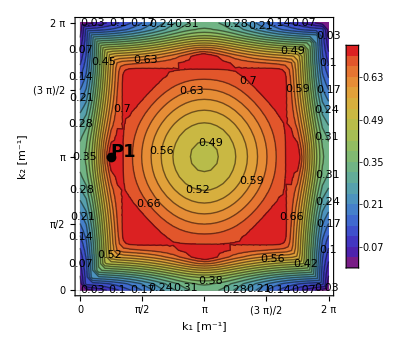
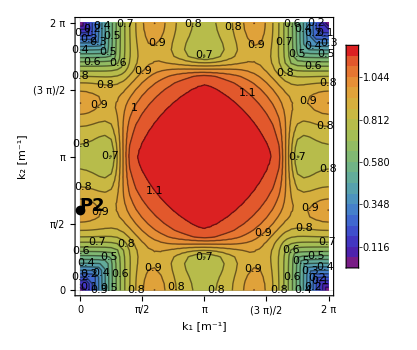
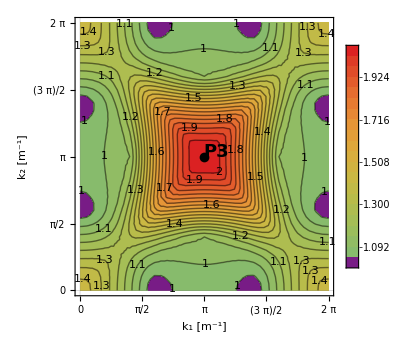
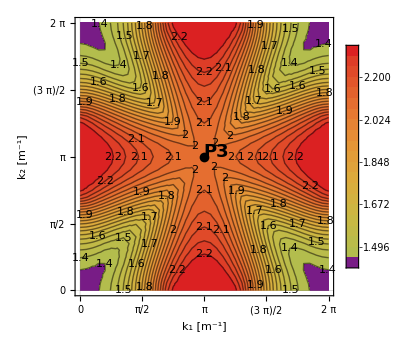
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
plot11[k_]:=Module[{},
If[k==3,
k0=k;
max=Max[data2[[;;800,k]]];
pos=Position[data2[[All,k]],max][[1]];
pos1=pos;
point=data2[[pos1,{1,2}]][[1]];,
If[k==4,
k0=k;
max=Max[data2[[;;41,k]]];
pos=Position[data2[[All,k]],max][[1]];
pos2=pos;
point=data2[[pos,{1,2}]][[1]],
If[k==5,
k0=k;
max=Max[data2[[All,k]]];
pos=Position[data2[[All,k]],max][[1]];
pos3=pos;
point=data2[[pos,{1,2}]][[1]];,
If[k==6,
k0=k-1;
point={Pi, Pi};
]
]
]
];
Show[
ListContourPlot[
Transpose[{data2[[All, 1]], data2[[All, 2]], data2[[All, k]]}],
 FrameLabel->{"k_1 [m^-1]", "k_2 [m^-1]" }, ImageSize->350, PlotLegends->Automatic, ContourLabels->All, Contours->20,ColorFunction->"Rainbow",
FrameTicks->{Table[p,{p,0,2*Pi,Pi/4}],Table[p,{p,0,2*Pi,Pi/4}]},
PlotTheme->"Scientific"
],
Graphics[
{Black, PointSize[.02], Point[point],
Text[Style["P"<>ToString[k0-2], FontSize->18, FontWeight->Bold],point+{.3,.1}]
}]
]
];
Grid[{{plot11[3], plot11[4], plot11[5], plot11[6]}}]
```

```mathematica
ClearAll[p];
data2[[pos2,;;3]]

p1 = {{π/4, π, data2[[pos1,3]][[1]]}};
p2 = {{0,  data2[[pos2,2]][[1]], data2[[pos2,4]][[1]]}};
p3 = {{π, π,  data2[[pos3,5]][[1]]}};

p =Join[p1,p2,p3];
p =Transpose[Prepend[Transpose[p], {"P_1", "P_2", "P_3"}]];
p = Transpose[Append[Transpose[p], {"I-II", "II-III", "III-IV"}]];

title5 = "Posizione e valore dei punti critici rappresentati sulle superfici di dispersione";

head5 ={{},{"Point", "k_1L_1[-]", "k_2L_1[-]", "ω/ω_ref[-]", "Dispersion surface"}};
tab5=(Grid[{
{Item[#1,Alignment->Center]},
{TableForm[#2,TableHeadings->#3, TableAlignments->Center]}},
Dividers->None]&@@@{{title5,p,head5}})[[1]]
```

{{0,1.88496,0.215327}}

Posizione e valore dei punti critici rappresentati sulle superfici di dispersione
 | Point | k_1L_1[-] | k_2L_1[-] | ω/ω_ref[-] | Dispersion surface
 | P_1 | π/4 | π | 0.741478 | I-II
 | P_2 | 0 | 1.88496 | 0.988217 | II-III
 | P_3 | π | π | 2.08338 | III-IV

## Plot imaginary part

```mathematica
dataim= Import["./export/imag_2D_20.dat"];

Show[
ListPlot3D[
Table[
Transpose[{dataim[[All, 1]], dataim[[All, 2]], dataim[[All, j]]}],
{j,5,5}
],
 AxesLabel->{"k_1 [m^-1]", "k_2 [m^-1]","Im(ω/ω_ref) [-]" }, Mesh->Automatic, ImageSize->imgsize,ColorFunction->"Rainbow", PlotLegends->Automatic,
Ticks->{Table[k,{k,0,2*Pi, Pi/2}],Table[k,{k,0,2*Pi, Pi/2}], Automatic},
PlotTheme->"Scientific"
]
(*,Graphics3D[
{Red,PointSize[.02] ,Point[
{{6.283185307179586,4.39822971502571,0.9882168607491879}}
]}
]*)
,BoxRatios->{1, 1, 2},
PlotRange->{Automatic,Automatic, Automatic}
]
```

-Graphics3D-

## Shear type beam mode shapes

```mathematica
ClearAll[α, v, x, L, c1, c2, c3, c4, EJ, RR, MM, αcr, Pcr,k];
v[x_]:=c1+c2*x+c3*Cos[α*x]+c4*Sin[α*x];

L=1;
EJ=1;
{RR, MM} = CoefficientArrays[
{
v[0]==0,
v'[0]==0,
-(v'''[L]+α^2*v'[L])==0,
v'[L]==0
},
{c1,c2,c3,c4}
]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0
0 | 1 | 0 | α
0 | -α^2 | 0 | 0
0 | 1 | -α Sin[α] | α Cos[α])

(0
0
0
0)

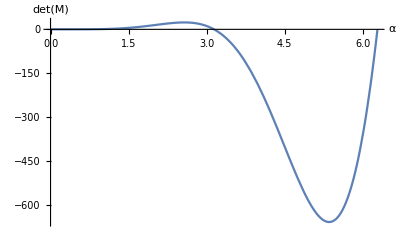

```mathematica
Plot[Det[MM], {α, 0, 2Pi}, AxesLabel->{"α", "det(M)"}]
```

```mathematica
FindRoot[Det[MM]==0, {α, Pi}]
```

{α→3.14159}

```mathematica
αcr = Table[k*Pi, {k, 3}]
```

{π,2 π,3 π}

```mathematica
MMcr = MM/.α->αcr[[3]];
MatrixForm[MMcr]
```

(1 | 0 | 1 | 0
0 | 1 | 0 | 3 π
0 | -9 π^2 | 0 | 0
0 | 1 | 0 | -3 π)

```mathematica
csol={c2,c3,c4}/.Solve[MMcr.{c1,c2,c3,c4}==RR][[1]]
PrependTo[csol, c1];
csol
```

{0,-c1,0}

{c1,0,-c1,0}

```mathematica
vsol[x_]:=v[x]/.{c1->csol[[1]], c2->csol[[2]], c3->csol[[3]], c4->csol[[4]]}/.{c1->1, α->αcr[[3]]}
vsol[x]
```

1-Cos[3 π x]

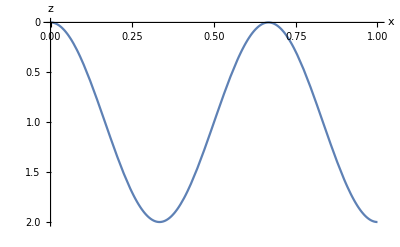

```mathematica
Plot[vsol[x], {x, 0, L}, AxesLabel->{"x", "z"}, ScalingFunctions->"Reverse"]
```